```mathematica
f[L_]:=FindRoot [Cos[x*L]-Cos[x]-2000.0*Sin[x]/(x),{x,800}]
```

```mathematica
x/.f[0.2]
```

801.106

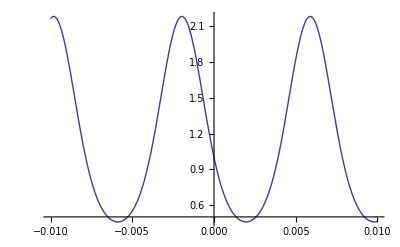

```mathematica
Plot[(Sin[(x/.f[L])*0.5*(1-L)])^2/(Sin[(x/.f[L])*0.5*(1+L)])^2,{L,-0.01, 0.01}]
```

```mathematica
[]
```

```mathematica
JurassicPark=ToRules[p2==0.00001 && p1 ==0.01 && p3 ==0.01 && A==1000]
```

{p2→0.00001,p1→0.01,p3→0.01,A→1000}

```mathematica
c[L_]:=(2 ⅇ^(-2 ⅈ (x/.f[L]) 0.5*(1+L)) (4+(-1+ⅇ^(2 ⅈ (x/.f[L]) 0.5*(1-L))) (x/.f[L])^2*A*A*p2 p3-2 ⅈ (x/.f[L])*A*(p2+p3)))/(ⅇ^(-2 ⅈ (x/.f[L])*L) (x/.f[L])^2*A*A*(2-ⅈ (x/.f[L])*A*p1) p2 p3+ⅇ^(2 ⅈ (x/.f[L]) 0.5*(1-L)) (x/.f[L])^2*A*A*p1 (2+ⅈ (x/.f[L])*A*p2) p3+(x/.f[L])^2*A*A*p1 p2 (2-ⅈ (x/.f[L])*A*p3)+ⅈ ⅇ^(-2 ⅈ (x/.f[L]) 0.5*(1+L)) (2 ⅈ+(x/.f[L])*A*p1) (2 ⅈ+(x/.f[L])*A*p2) (2 ⅈ+(x/.f[L])*A*p3)) /. JurassicPark
```

```mathematica
d[L_]:=(2 ⅇ^(-2 ⅈ (x/.f[L]) 0.5*(1+L)) (x/.f[L])*A*(ⅇ^(2 ⅈ (x/.f[L]) 0.5*(1-L)) (2+ⅈ (x/.f[L])*A*p2) p3+p2 (2-ⅈ (x/.f[L])*A*p3)))/(-ⅇ^(-2 ⅈ (x/.f[L]) L) (x/.f[L])^2*A*A*(2 ⅈ+(x/.f[L])*A*p1) p2 p3+ⅇ^(2 ⅈ (x/.f[L]) 0.5*(1-L)) (x/.f[L])^2*A*A*p1 (-2 ⅈ+(x/.f[L])*A*p2) p3-(x/.f[L])^2*A*A*p1 p2 (2 ⅈ+(x/.f[L])*A*p3)+ⅇ^(-2 ⅈ (x/.f[L]) 0.5*(1+L)) (2 ⅈ+(x/.f[L])*A*p1) (2 ⅈ+(x/.f[L])*A*p2) (2 ⅈ+(x/.f[L])*A*p3)) /. JurassicPark
```

```mathematica
e[L_]:=(4 ⅇ^(-2 ⅈ (x/.f[L]) 0.5*(1+L)) (2 ⅈ+(x/.f[L])*A*p3))/(ⅇ^(-2 ⅈ (x/.f[L]) L) (x/.f[L])^2*A*A*(2 ⅈ+(x/.f[L])*A*p1) p2 p3-ⅇ^(2 ⅈ (x/.f[L]) 0.5*(1-L)) (x/.f[L])^2*A*A*p1 (-2 ⅈ+(x/.f[L])*A*p2) p3+(x/.f[L])^2*A*A*p1 p2 (2 ⅈ+(x/.f[L])*A*p3)-ⅇ^(-2 ⅈ(x/.f[L]) 0.5*(1+L)) (2 ⅈ+(x/.f[L])*A*p1) (2 ⅈ+(x/.f[L])*A*p2) (2 ⅈ+(x/.f[L])*A*p3)) /. JurassicPark
```

```mathematica
g[L_]:=-(4 ⅇ^(-2 ⅈ (x/.f[L]) L) (x/.f[L])*A*p3)/(ⅇ^(-2 ⅈ (x/.f[L]) L) (x/.f[L])^2*A*A*(2 ⅈ+(x/.f[L])*A*p1) p2 p3-ⅇ^(2 ⅈ (x/.f[L]) 0.5*(1-L)) (x/.f[L])^2*A*A*p1 (-2 ⅈ+(x/.f[L])*A*p2) p3+(x/.f[L])^2*A*A*p1 p2 (2 ⅈ+(x/.f[L])*A*p3)-ⅇ^(-2 ⅈ (x/.f[L]) 0.5*(1+L)) (2 ⅈ+(x/.f[L])*A*p1) (2 ⅈ+(x/.f[L])*A*p2) (2 ⅈ+(x/.f[L])*A*p3)) /. JurassicPark
```

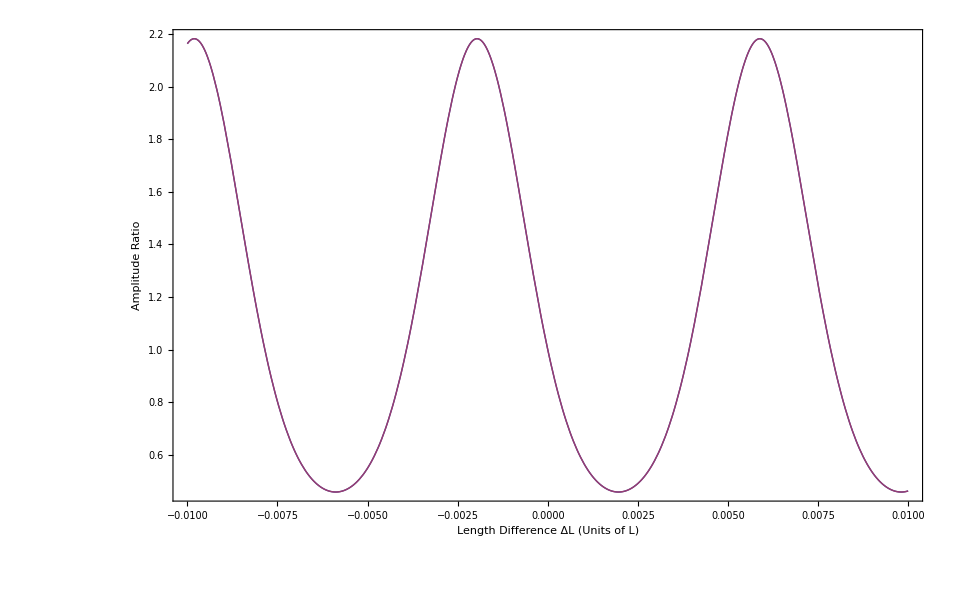

```mathematica
Plot[{(c[L]*(Conjugate[c[L]]) + d[L]*(Conjugate[d[L]])  )/(e[L]*(Conjugate[e[L]]) +g[L]*(Conjugate[g[L]]) ),(Sin[(x/.f[L])*0.5*(1-L)])^2/(Sin[(x/.f[L])*0.5*(1+L)])^2},{L,-0.01,0.01},Frame->True,LabelStyle->Directive[FontFamily->"Times",FontSize->16],FrameLabel->{"Length Difference ΔL (Units of L)","Amplitude Ratio"}]
```

```mathematica
t2[L_]:=(8 ⅇ^(-2 ⅈ (x/.f[L]) 0.5*(1+L)))/(ⅇ^(-2 ⅈ (x/.f[L]) L) (x/.f[L])^2*A*A (2-ⅈ (x/.f[L])*A p1) p2 p3+ⅇ^(2 ⅈ (x/.f[L]) 0.5*(1-L)) (x/.f[L])^2*A*A p1 (2+ⅈ (x/.f[L])*A p2) p3+(x/.f[L])^2*A*A p1 p2 (2-ⅈ (x/.f[L])*A p3)+ⅈ ⅇ^(-2 ⅈ (x/.f[L]) 0.5*(1+L)) (2 ⅈ+(x/.f[L])*A p1) (2 ⅈ+(x/.f[L])*A p2) (2 ⅈ+(x/.f[L])*A p3)) /. JurassicPark
```

```mathematica
t1[L_]:=-(ⅇ^(-2 ⅈ (x/.f[L]) 0.5*(1+L)) (x/.f[L])*A (ⅇ^(-2 ⅈ (x/.f[L]) L) (x/.f[L])^2*A*A p1 p2 p3-ⅇ^(2 ⅈ (x/.f[L]) 0.5*(1-L)) (-2 ⅈ+(x/.f[L])*A p1) (-2 ⅈ+(x/.f[L])*A p2) p3+(-2 ⅈ+(x/.f[L])*A p1) p2 (2 ⅈ+(x/.f[L])*A p3)-ⅇ^(-2 ⅈ (x/.f[L]) 0.5*(1+L)) p1 (2 ⅈ+(x/.f[L])*A p2) (2 ⅈ+(x/.f[L])*A p3)))/(ⅇ^(-2 ⅈ (x/.f[L]) L) (x/.f[L])^2*A*A (2 ⅈ+(x/.f[L])*A p1) p2 p3-ⅇ^(2 ⅈ (x/.f[L]) 0.5*(1-L)) (x/.f[L])^2*A*A p1 (-2 ⅈ+(x/.f[L])*A p2) p3+(x/.f[L])^2*A*A p1 p2 (2 ⅈ+(x/.f[L])*A p3)-ⅇ^(-2 ⅈ (x/.f[L]) 0.5*(1+L)) (2 ⅈ+(x/.f[L])*A p1) (2 ⅈ+(x/.f[L])*A p2) (2 ⅈ+(x/.f[L])*A p3)) /. JurassicPark
```

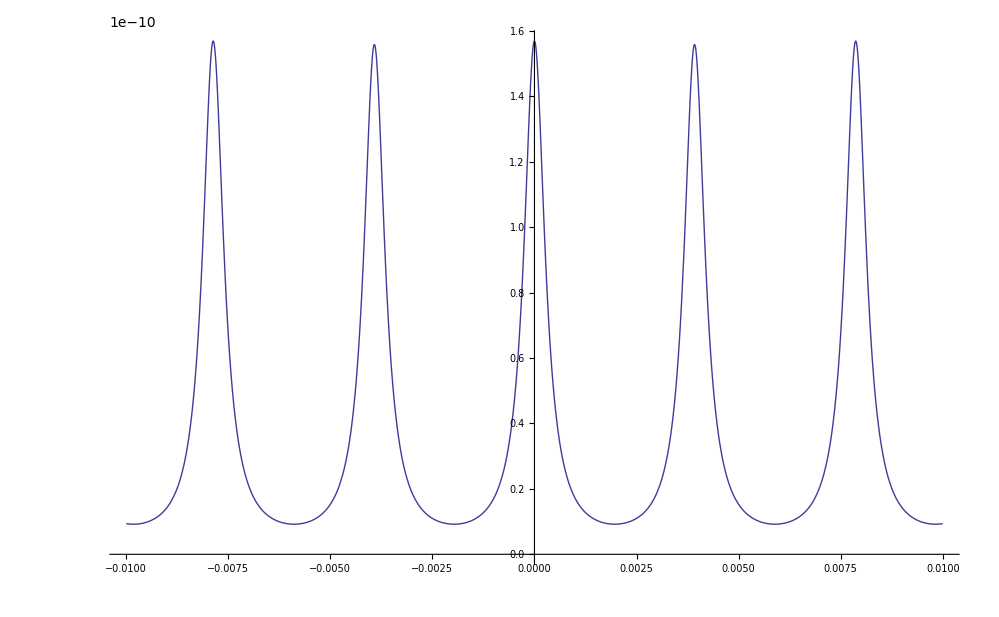

```mathematica
Plot[{(t2[L]*(Conjugate[t2[L]]) )},{L,-0.01,0.01}]
```

```mathematica
t3[L_,x_]:=(8 ⅇ^(-2 ⅈ x 0.5*(1+L)))/(ⅇ^(-2 ⅈ x L) x^2*A*A (2-ⅈ x*A p1) p2 p3+ⅇ^(2 ⅈ x 0.5*(1-L)) x^2*A*A p1 (2+ⅈ x*A p2) p3+x^2*A*A p1 p2 (2-ⅈ x*A p3)+ⅈ ⅇ^(-2 ⅈ x 0.5*(1+L)) (2 ⅈ+x*A p1) (2 ⅈ+x*A p2) (2 ⅈ+x*A p3)) /.JurassicPark
```

```mathematica
Plot3D[(t3[L,x]*(Conjugate[t3[L,x]]) ), {L,-0.01,0.01},{x,795,805},PlotRange->{0,1}] (*p2->1.*^-6,p1->0.00001,p3->0.00001,A->1000*)
```

-Graphics3D-

```mathematica
t4[L_,x_]:=-(ⅇ^(-2 ⅈ x 0.5*(1+L)) x*A (ⅇ^(-2 ⅈ x L) x^2*A*A p1 p2 p3-ⅇ^(2 ⅈ x 0.5*(1-L)) (-2 ⅈ+x*A p1) (-2 ⅈ+x*A p2) p3+(-2 ⅈ+x*A p1) p2 (2 ⅈ+x*A p3)-ⅇ^(-2 ⅈ x 0.5*(1+L)) p1 (2 ⅈ+x*A p2) (2 ⅈ+x*A p3)))/(ⅇ^(-2 ⅈ x L) x^2*A*A (2 ⅈ+x*A p1) p2 p3-ⅇ^(2 ⅈ x 0.5*(1-L)) x^2*A*A p1 (-2 ⅈ+x*A p2) p3+x^2*A*A p1 p2 (2 ⅈ+x*A p3)-ⅇ^(-2 ⅈ x 0.5*(1+L)) (2 ⅈ+x*A p1) (2 ⅈ+x*A p2) (2 ⅈ+x*A p3)) /. JurassicPark
```

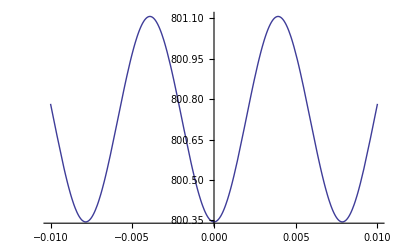

```mathematica
v1=Plot[x/. f[L],{L,-0.01,0.01}]
```

```mathematica
M1[L_]:=x/.Last[FindMaximum[{(t3[L,x]*(Conjugate[t3[L,x]]) ),799<x<802},x]]
```

```mathematica
v2=ContourPlot[(t3[L,x]*(Conjugate[t3[L,x]]) ), {L,-0.01,0.01},{x,795,805},PlotRange->{0,1}](*p2->1.*^-6,p1->0.00001,p3->0.00001,A->1000*)
```

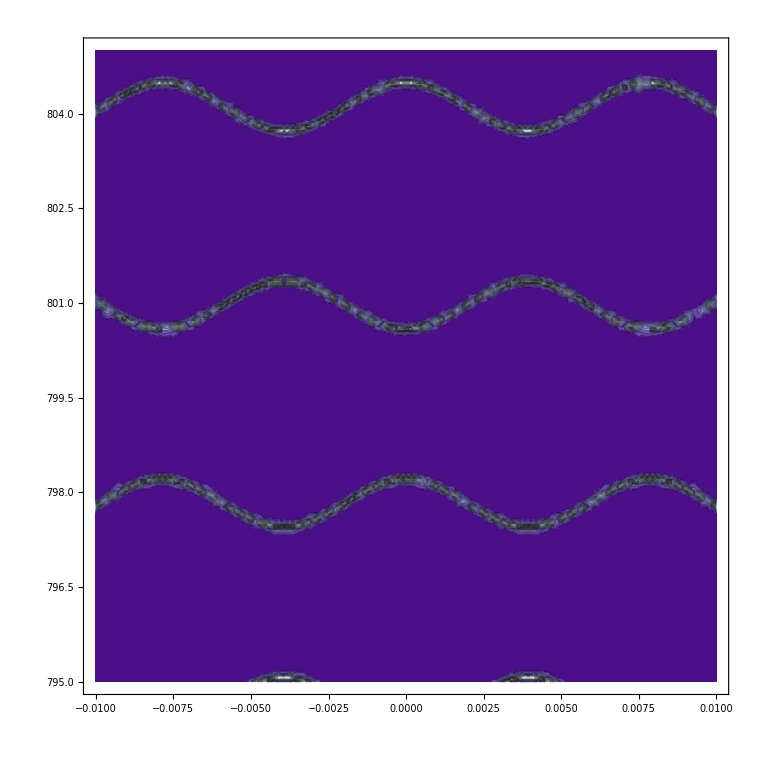
```mathematica
-Graphics-JurassicPark=ToRules[p2==0.000001 && p1 ==0.01 && p3 ==0.01 && A==1000]
```

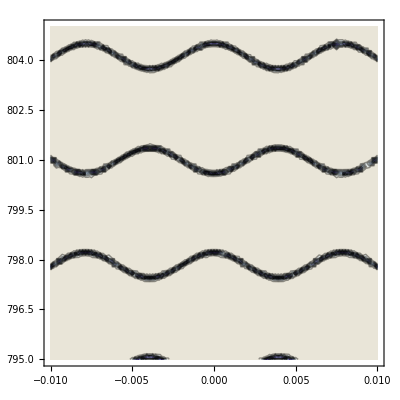

```mathematica
v3=ContourPlot[(t4[L,x]*(Conjugate[t4[L,x]]) ), {L,-0.01,0.01},{x,795,805},PlotRange->{0,1}](*p2->1.*^-6,p1->0.00001,p3->0.00001,A->1000*)
```

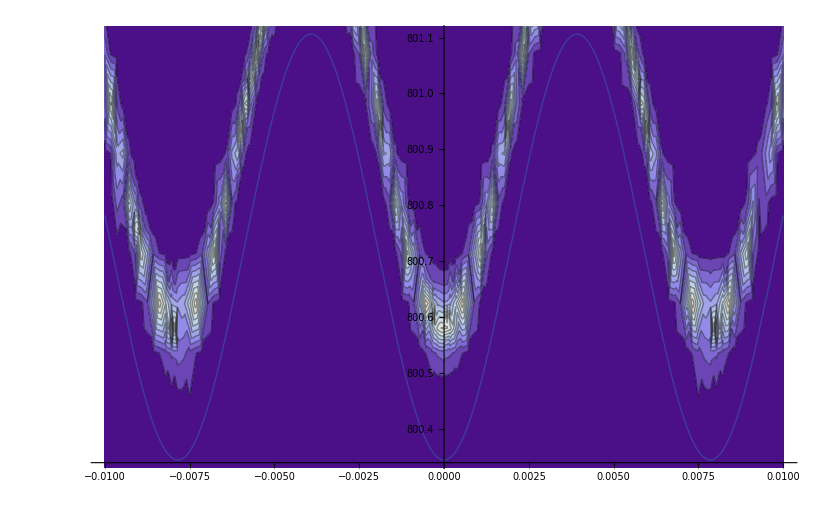

```mathematica
Show[v1,v2,v5](*p2->1.*^-6,p1->0.00001,p3->0.00001,A->1000*)
```

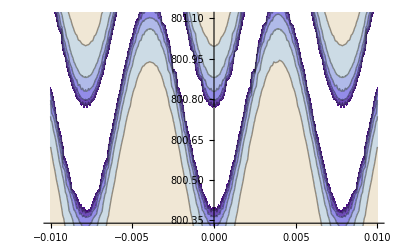

```mathematica
Show[v1,v3]
```

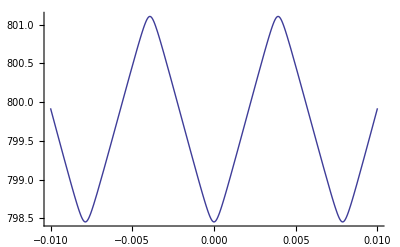

```mathematica
v5=Plot[x/. f[L],{L,-0.01,0.01}]
```

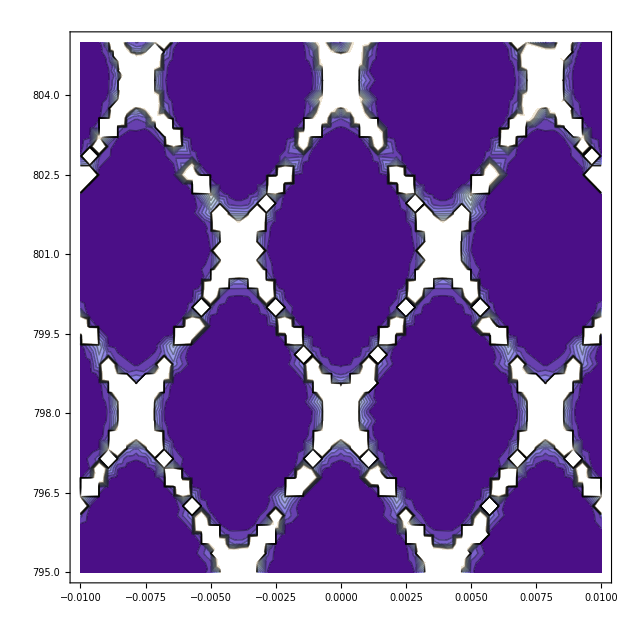

```mathematica
ContourPlot[(t3[L,x]*(Conjugate[t3[L,x]]) ), {L,-0.01,0.01},{x,795,805}]
```

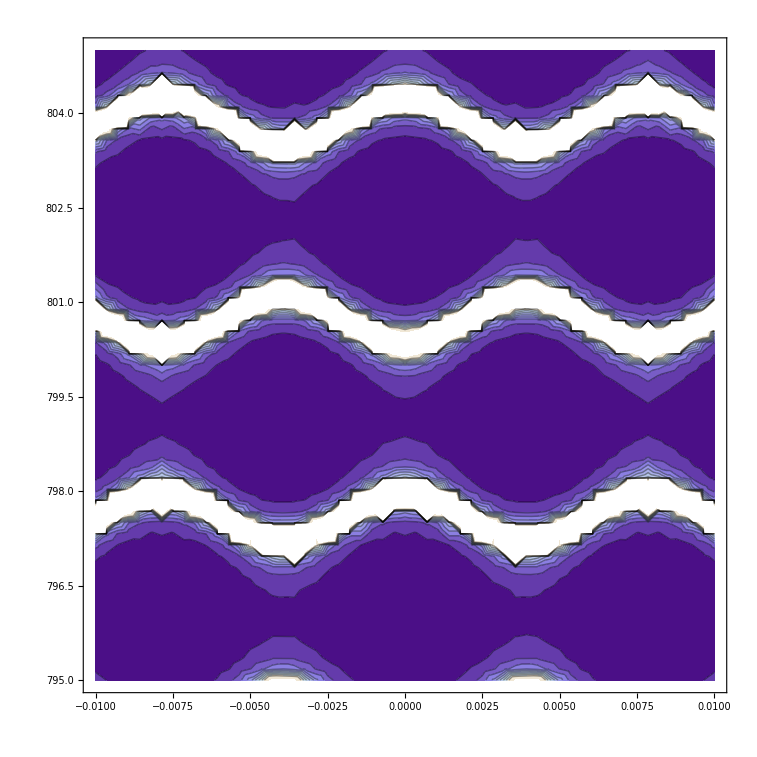

```mathematica
ContourPlot[(t3[L,x]*(Conjugate[t3[L,x]]) ), {L,-0.01,0.01},{x,795,805}]
```

```mathematica
M1[L_]:=x/.Last[NMaximize[{(t3[L,x]*(Conjugate[t3[L,x]]) ),799<x<802},x]]
```

Greater::nord: Invalid comparison with 0.  + 0.\ ⅈ
 attempted.

Less::nord: Invalid comparison with 0.00382954  + 0.\ ⅈ
 attempted.

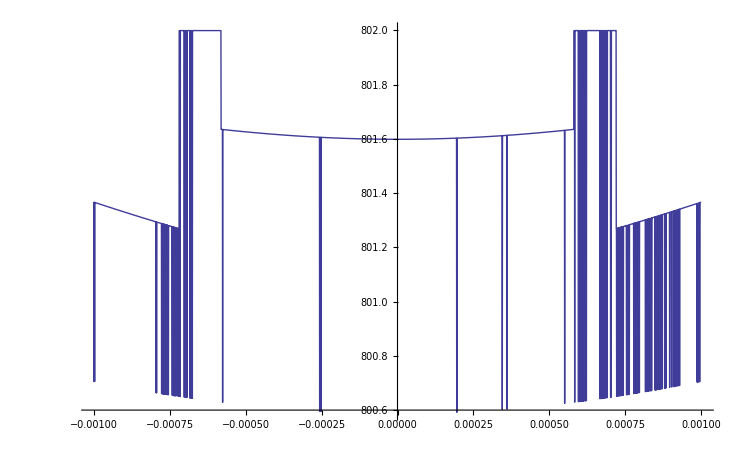

```mathematica
Plot[M1[L],{L,-0.001,0.001}]
```

```mathematica
Re[(t3[0,800.65]*(Conjugate[t3[0,800.65]]) )]
```

0.194795

```mathematica
Plot3D[(t3[L,x]*(Conjugate[t3[L,x]]) ), {L,-0.001,0.001},{x,800.6,800.8}]
```

-Graphics3D-

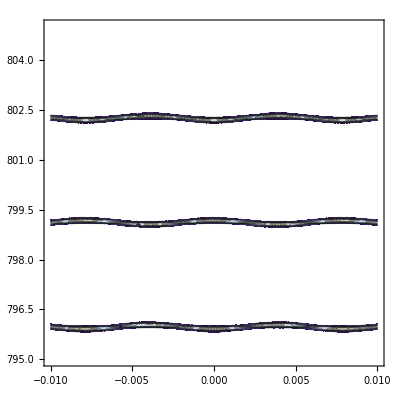

```mathematica
v6=ContourPlot[(t3[L,x]*(Conjugate[t3[L,x]]) ), {L,-0.01,0.01},{x,795,805},PlotRange->{0.993,1}](*p2->1.*^-7,p1->0.000001,p3->0.000001,A->1000*)
```

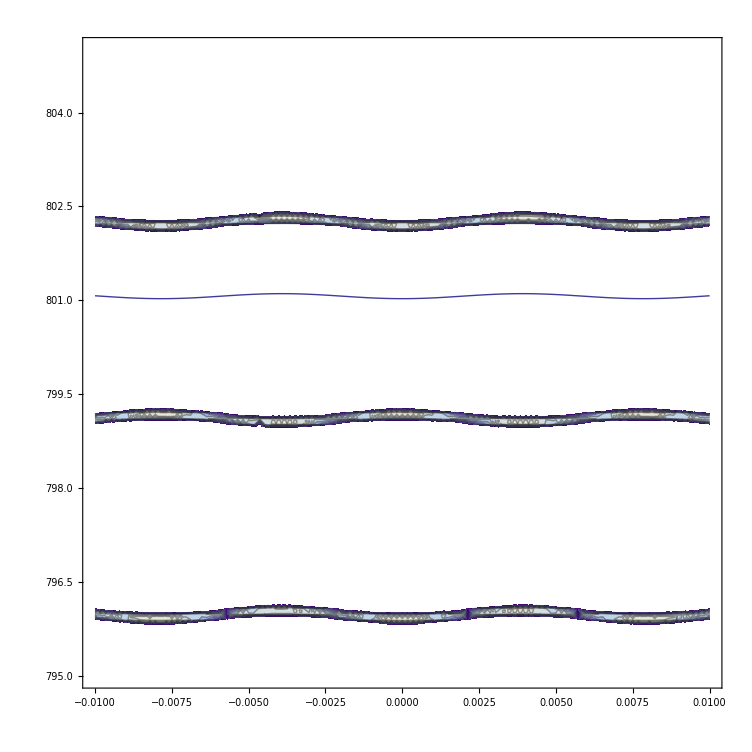

```mathematica
Show[v6,v5]
```

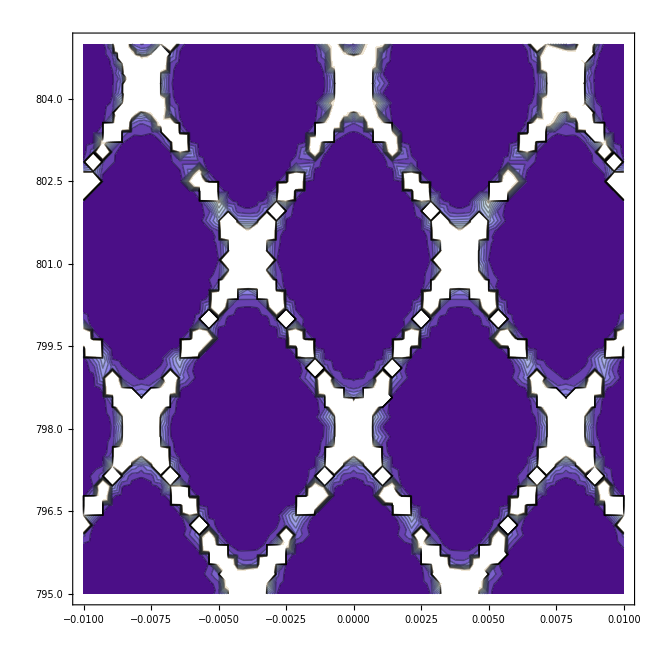

```mathematica
v7=ContourPlot[(t3[L,x]*(Conjugate[t3[L,x]]) ), {L,-0.01,0.01},{x,795,805}](*p2->1.*^-5,p1->0.001,p3->0.001,A->1000*)
```

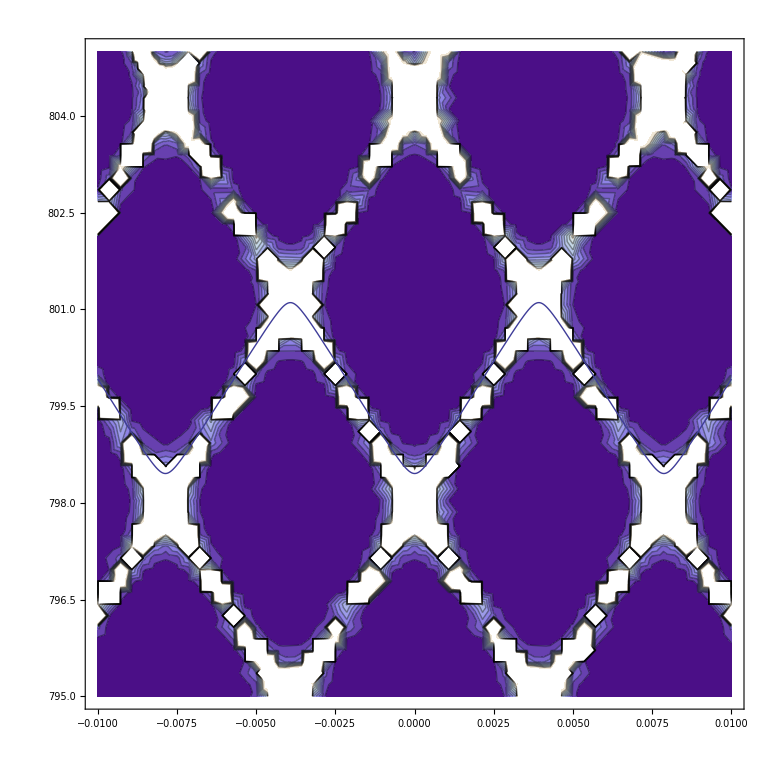

```mathematica
Show[v7,v5]
```

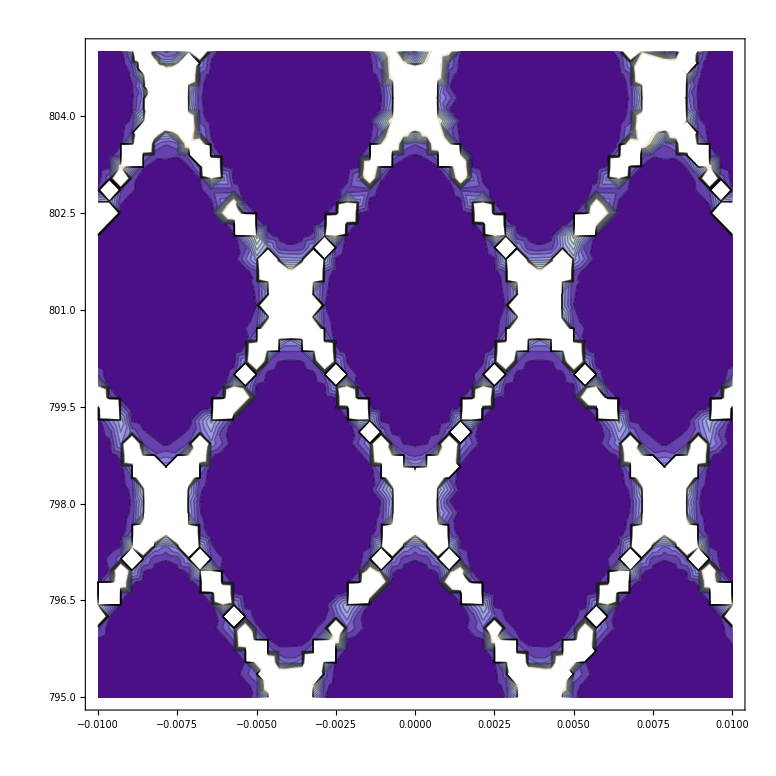

```mathematica
v8=ContourPlot[(t3[L,x]*(Conjugate[t3[L,x]]) ), {L,-0.01,0.01},{x,795,805}](*p2->1.*^-4,p1->0.001,p3->0.001,A->1000*)
```

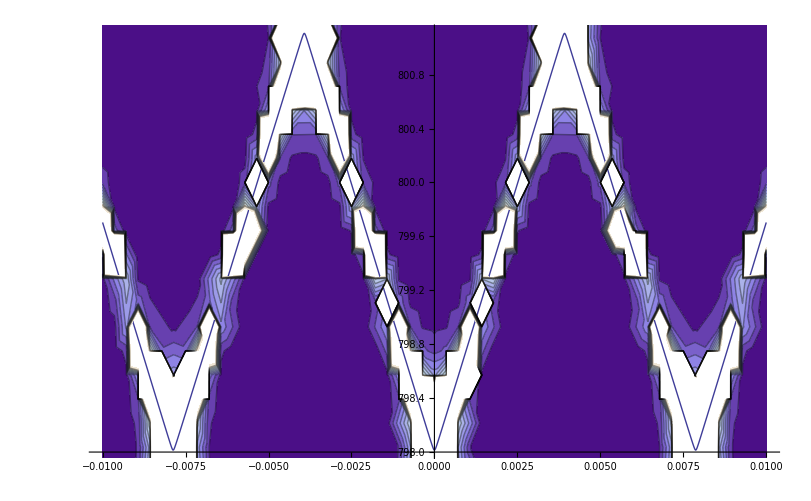

```mathematica
Show[v1,v8]
```

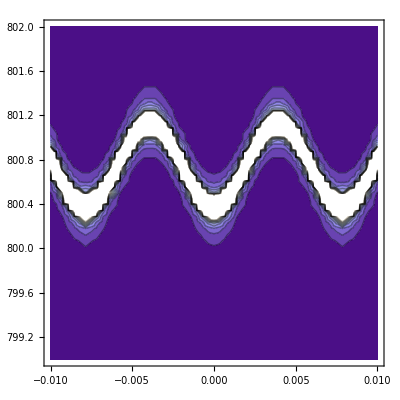

```mathematica
v9=ContourPlot[(t3[L,x]*(Conjugate[t3[L,x]]) ), {L,-0.01,0.01},{x,799,802},PlotRange->{0,0.00001}](*p2->1.*^-6,p1->0.0001,p3->0.0001,A->1000*)
```

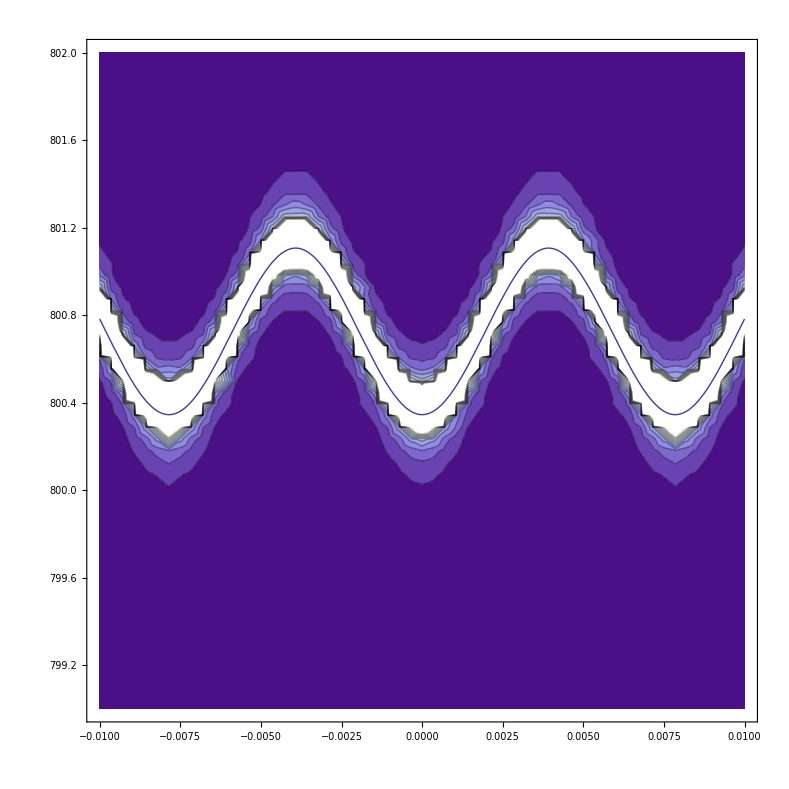

```mathematica
Show[v9,v1]
```

```mathematica
M1[L_]:=x/.Last[NMaximize[{Re[(t3[L,x]*(Conjugate[t3[L,x]]) )],799<x<802},{x},WorkingPrecision->40]]
```

```mathematica
M1[0]
```

NMaximize::precw: The precision of the argument function (64\ Re[ⅇ^(0.  - 1.\ ⅈ)\ x + (0.  + 1.\ ⅈ)\ Conjugate[x]/(ⅈ\ ⅇ^(0.  - 1.\ ⅈ)\ x\ (2\ ⅈ + 0.001\ x)\ (2\ ⅈ + Times[« 2 »])^2 + 0.01\ ⅇ^(0.  + 1.\ ⅈ)\ x\ (2 + (0.  + 0.001\ ⅈ)\ x)\ x^2 + 0.0002\ (2 - (0.  + 0.1\ ⅈ)\ x)\ x^2)\ Conjugate[ⅈ\ ⅇ^Times[« 2 »]\ (2\ ⅈ + Times[« 2 »])\ Plus[« 2 »]^2 + 0.01\ ⅇ^Times[« 2 »]\ (2 + Times[« 2 »])\ x^2 + 0.0002\ (2 + Times[« 2 »])\ x^2]]
) is less than WorkingPrecision (40).

800.3697783882314535034785879808694639595

NMaximize::precw: The precision of the argument function (64\ Re[ⅇ^(0.  - 0.999\ ⅈ)\ x + (0.  + 0.999\ ⅈ)\ Conjugate[x]/(ⅈ\ ⅇ^(0.  - 0.999\ ⅈ)\ x\ (2\ ⅈ + 0.001\ x)\ (2\ ⅈ + Times[« 2 »])^2 + 0.01\ ⅇ^(0.  + 1.001\ ⅈ)\ x\ (2 + (0.  + 0.001\ ⅈ)\ x)\ x^2 + 0.0001\ (2 - (0.  + 0.1\ ⅈ)\ x)\ x^2 + 0.0001\ ⅇ^(0.  + 0.00199992\ ⅈ)\ x\ (2 - (0.  + 0.1\ ⅈ)\ x)\ x^2)\ Conjugate[ⅈ\ ⅇ^Times[« 2 »]\ (2\ ⅈ + Times[« 2 »])\ Plus[« 2 »]^2 + 0.01\ ⅇ^« 1 »\ « 1 »\ x^2 + « 1 » + 0.0001\ ⅇ^Times[« 2 »]\ (2 + Times[« 2 »])\ x^2]]
) is less than WorkingPrecision (40).

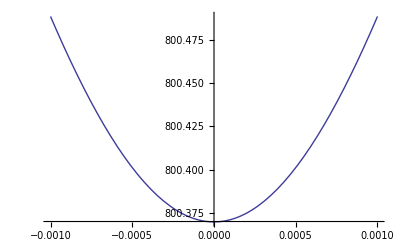

```mathematica
b1=Plot[M1[L],{L,-0.001,0.001}]
```

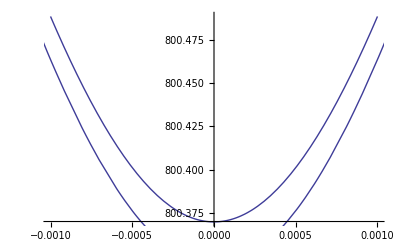

```mathematica
Show[b1,v1](*{p2->1.*^-6,p1->0.0001,p3->0.0001,A->1000}*)
```

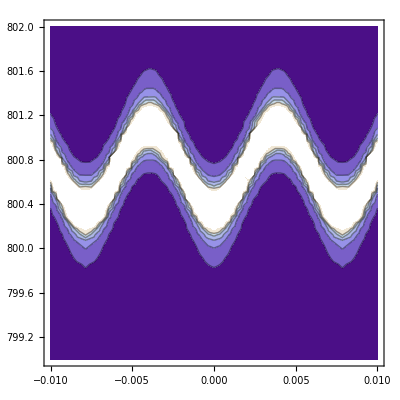

```mathematica
ContourPlot[(t3[L,x]*(Conjugate[t3[L,x]]) ), {L,-0.01,0.01},{x,799,802}](*p2->1.*^-6,p1->0.0001,p3->0.0001,A->1000*)
```

NMaximize::precw: The precision of the argument function (64\ Re[ⅇ^(0.  - 0.999\ ⅈ)\ x + (0.  + 0.999\ ⅈ)\ Conjugate[x]/(1.\ ⅇ^(0.  + 1.001\ ⅈ)\ x\ (2 + (0.  + 0.001\ ⅈ)\ x)\ x^2 + 0.001\ (2 - (0.  + 1.\ ⅈ)\ x)\ x^2 + 0.001\ ⅇ^(0.  + 0.00199992\ ⅈ)\ x\ (2 - (0.  + 1.\ ⅈ)\ x)\ x^2 + ⅈ\ ⅇ^(0.  - 0.999\ ⅈ)\ x\ (2\ ⅈ + 0.001\ x)\ (2\ ⅈ + Times[« 2 »])^2)\ Conjugate[1.\ ⅇ^Times[« 2 »]\ (2 + Times[« 2 »])\ x^2 + 0.001\ (2 + Times[« 2 »])\ x^2 + 0.001\ ⅇ^« 1 »\ « 1 »\ x^2 + ⅈ\ ⅇ^Times[« 2 »]\ (2\ ⅈ + Times[« 2 »])\ Plus[« 2 »]^2]]
) is less than WorkingPrecision (40).

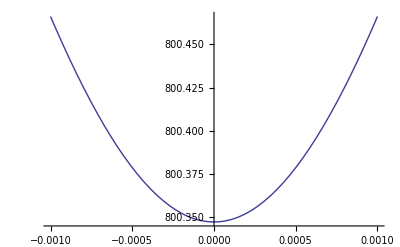

```mathematica
b2=Plot[M1[L],{L,-0.001,0.001}]
```

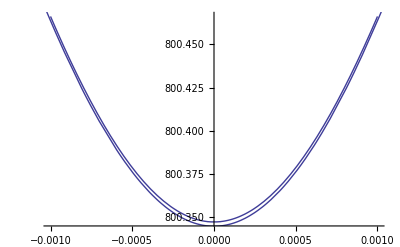

```mathematica
Show[b2,v1](*{p2->1.*^-6,p1->0.001,p3->0.001,A->1000}*)
```

NMaximize::precw: The precision of the argument function (64\ Re[ⅇ^(0.  - 0.999\ ⅈ)\ x + (0.  + 0.999\ ⅈ)\ Conjugate[x]/(100.\ ⅇ^(0.  + 1.001\ ⅈ)\ x\ (2 + (0.  + 0.001\ ⅈ)\ x)\ x^2 + 0.01\ (2 - (0.  + 10.\ ⅈ)\ x)\ x^2 + 0.01\ ⅇ^(0.  + 0.00199992\ ⅈ)\ x\ (2 - (0.  + 10.\ ⅈ)\ x)\ x^2 + ⅈ\ ⅇ^(0.  - 0.999\ ⅈ)\ x\ (2\ ⅈ + 0.001\ x)\ (2\ ⅈ + Times[« 2 »])^2)\ Conjugate[100.\ ⅇ^Times[« 2 »]\ (2 + Times[« 2 »])\ x^2 + 0.01\ (2 + Times[« 2 »])\ x^2 + 0.01\ « 1 »\ « 1 »\ x^2 + ⅈ\ ⅇ^Times[« 2 »]\ (2\ ⅈ + Times[« 2 »])\ Plus[« 2 »]^2]]
) is less than WorkingPrecision (40).

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

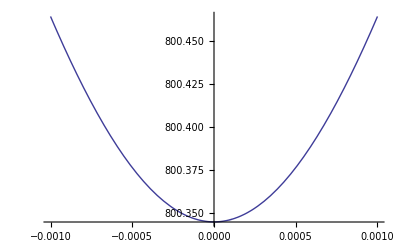

```mathematica
b3=Plot[M1[L],{L,-0.001,0.001}](*{p2->1.*^-6,p1->0.01,p3->0.01,A->1000}*)
```

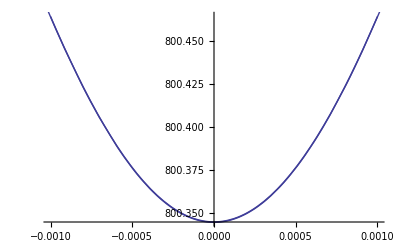

```mathematica
Show[b3,v1](*{p2->1.*^-6,p1->0.01,p3->0.01,A->1000}*)
```